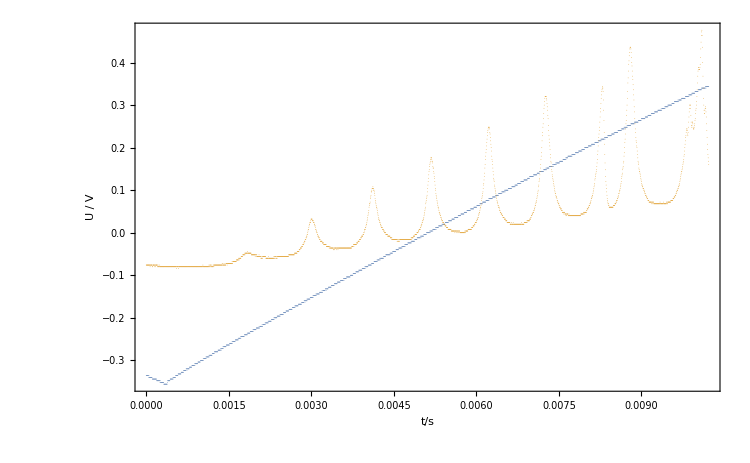

```mathematica
path="./up-etalon_zoom.tab";
data=Drop[Import[path],1];
ch1=Transpose[{data[[All,1]],data[[All,2]]}];
ch2=Transpose[{data[[All,1]],data[[All,3]]}];
ListPlot[{ch1,ch2},PlotRange->All,Frame->True,ImageSize->750,PlotStyle->{PointSize[0.0001]},FrameLabel->{"t/s","U / V"}]
```

{0.005,0.0054}

FittedModel[-0.272836+(1.61265×10^-9)/(8.5072×10^-9+(-«21»+x)^2)+49.8682 x]

| Estimate | Standard Error | t-Statistic | P-Value
a | -0.272836 | 0.0151578 | -17.9997 | 9.45197×10^-29
b | 49.8682 | 2.83137 | 17.6127 | 3.49582×10^-28
c | 0.0000174842 | 2.65392×10^-7 | 65.8807 | 1.86736×10^-67
t | 0.00518218 | 3.55339×10^-7 | 14583.7 | 1.00255×10^-240
s | 0.0000922345 | 9.92221×10^-7 | 92.9576 | 2.18337×10^-78

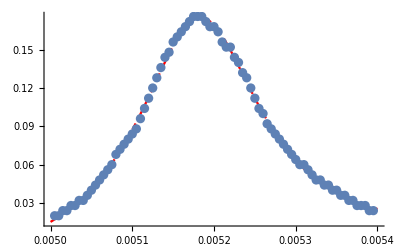

```mathematica
{xmin, xmax} = {0.005, 0.0054}
fitData = Select[ch2, #[[1]] >xmin && #[[1]] <  xmax&];
nlm = NonlinearModelFit[fitData,{a + b x + c s/(s^2+(x-t)^2)},{{a, -0.042},{b, 0},{c, 0.0000252}, {t,0.005181}, {s, 0.000118}}, x]
nlm["ParameterTable"]
Show[Plot[Normal[nlm], {x, xmin, xmax}, PlotRange->All, PlotStyle->{Red, Dashed}], ListPlot[fitData]]
```

```mathematica
Manipulate[Show[Plot[a + b x + c s/(s^2+(x-t)^2) ,{x, xmin, xmax}, PlotRange->All, PlotStyle->{Red, Dashed}], ListPlot[fitData]], {{a, -0.0485}, -0.2, 0}, {{b, 0}, 0, 1}, {{c, 0.0000294}, 0.00001, 0.0002}, {{t, 0.0052}, 0.0050, 0.0054}, {{s, 0.000126}, 0.00005, 0.0005}]
```